# Laboratorio TC2 (Intento 5)

-Graphics-

## Ecuaciones Planteadas

La primera ecuación es haciendo il=i(R2) y aplicando la transformada

```mathematica
(*           il=C1*Vc'[t] ; i(R2)=(Vn-Vo[t])/R2; Vn=Vo[t]*RB/(RA+RB) ;   i(R2)=Vo[t]/R2*(-Ra/(Ra+Rb)) ;   Vo[t]/R2*(-Ra/(Ra+Rb))  = C1*Vc'[t] ;                         *)
```

```mathematica
eq1=C1*s*Vc[s]-C1*v0[t]-Vo[s]*Ra/(R2*(Ra+Rb))==0;
```

Segunda ecuación

```mathematica
(*       Vl[t]=L*il'[t]; Vr[t]=il[t]*(R1+R2); Vo[t]=Vr[t]+Vc[t]+Vl[t];   Vo[t]= il[t](R1+R2)+L*il'[t]+Vc[t] ; il[t]=ic[t]=C*Vc'[t]; Vo[t]=C*(R1+R2)*Vc'[t]+L*C*Vc''[t]+Vc[t]     *)
```

```mathematica
eq2=Vc[s]-Vo[s]+C1*(R1+R2)*(s*Vc[s]-v0[t])+L1*C1*(s^2*Vc[s]-s*v0[t])==0
```

Vc[s]+C1 (R1+R2) (-v0[t]+s Vc[s])+C1 L1 (-s v0[t]+s^2 Vc[s])-Vo[s]==0

## Resolución

```mathematica
sol1=Solve[{eq1,eq2},{Vo[s],v0[t]}]
```

{{Vo[s]→(R2 (Ra+Rb) Vc[s])/(-R1 Ra+R2 Rb-L1 Ra s),v0[t]→-((-Ra Vc[s]-C1 R1 Ra s Vc[s]+C1 R2 Rb s Vc[s]-C1 L1 Ra s^2 Vc[s])/(C1 (R1 Ra-R2 Rb+L1 Ra s)))}}

```mathematica
Vo[s]=Extract[sol1,{1,1,2}]
```

(R2 (Ra+Rb) Vc[s])/(-R1 Ra+R2 Rb-L1 Ra s)

```mathematica
v0[t]=Extract[sol1,{1,2,2}]
```

-((-Ra Vc[s]-C1 R1 Ra s Vc[s]+C1 R2 Rb s Vc[s]-C1 L1 Ra s^2 Vc[s])/(C1 (R1 Ra-R2 Rb+L1 Ra s)))

## Función de transferencia

```mathematica
H[s]=FullSimplify[Vo[s]/v0[t]]
```

(C1 R2 (Ra+Rb))/(C1 R2 Rb s-Ra (1+C1 s (R1+L1 s)))

## Respuesta

```mathematica
respuesta=InverseLaplaceTransform[H[s],s,t]
```

(C1 (ⅇ^((-R1/(2 L1)+(R2 Rb)/(2 L1 Ra)-(√(-4 C1 L1 Ra^2+(C1 R1 Ra-C1 R2 Rb)^2))/(2 C1 L1 Ra)) t)-ⅇ^((-R1/(2 L1)+(R2 Rb)/(2 L1 Ra)+(√(-4 C1 L1 Ra^2+(C1 R1 Ra-C1 R2 Rb)^2))/(2 C1 L1 Ra)) t)) R2 (Ra+Rb))/(√(-4 C1 L1 Ra^2+(C1 R1 Ra-C1 R2 Rb)^2))

## Intento de poner más lindo todo u.u

```mathematica
Denominador=Collect[Simplify[Denominator[H[s]]/Ra],s^2]
```

-1+(-C1 R1+(C1 R2 Rb)/Ra) s-C1 L1 s^2

```mathematica
Numerador=Simplify[Numerator[H[s]]/Ra]
```

(C1 R2 (Ra+Rb))/Ra

```mathematica
Taof=Sqrt[C1*L1] ; ξf=Simplify[(C1 R1+2 C1 R2+(C1 R2 Rb)/Ra)/(2*Taof) ]
```

(C1 (R1+R2 (2+Rb/Ra)))/(2 √(C1 L1))

```mathematica
Hf[s]=Numerador/Denominador
```

(C1 R2 (Ra+Rb))/(Ra (-1+(-C1 R1+(C1 R2 Rb)/Ra) s-C1 L1 s^2))

```mathematica
Hf[s]=Hf[s]/.(C1 R2 (Ra+Rb))/Ra-> k
```

k/(-1+(-C1 R1+(C1 R2 Rb)/Ra) s-C1 L1 s^2)

```mathematica
Hf[s]=TransferFunctionModel[Hf[s],s]
```

k/(-1+(-C1 R1+(C1 R2 Rb)/Ra) s-C1 L1 s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11$CellContext`k$CellContext`Ra1FalseFalseFalseAutomaticNoneAutomatic

```mathematica
polosf=TransferFunctionPoles[Hf[s]]
```

{{{1/(2 C1 L1 Ra)(-C1 R1 Ra+C1 R2 Rb-√(-4 C1 L1 Ra^2+(-C1 R1 Ra+C1 R2 Rb)^2)),1/(2 C1 L1 Ra)(-C1 R1 Ra+C1 R2 Rb+√(-4 C1 L1 Ra^2+(-C1 R1 Ra+C1 R2 Rb)^2))}}}

```mathematica
pf1=Extract[polosf,{1,1,1}]
```

1/(2 C1 L1 Ra)(-C1 R1 Ra+C1 R2 Rb-√(-4 C1 L1 Ra^2+(-C1 R1 Ra+C1 R2 Rb)^2))

```mathematica
pf2=Extract[polosf,{1,1,2}]
```

1/(2 C1 L1 Ra)(-C1 R1 Ra+C1 R2 Rb+√(-4 C1 L1 Ra^2+(-C1 R1 Ra+C1 R2 Rb)^2))

## Ecuación genérica

```mathematica
Hg[s_]=k/(s^2*Tao^2+2*ξ*Tao*s+1)
```

k/(1+s^2 Tao^2+2 s Tao ξ)

```mathematica
Hg[s_]=TransferFunctionModel[Hg[s],s]
```

k/(1+2 Tao ξ s+Tao^2 s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11$CellContext`k11FalseFalseFalseAutomaticNoneAutomatic

```mathematica
polosg=TransferFunctionPoles[Hg[s]]
```

{{{(-Tao ξ-√(-Tao^2+Tao^2 ξ^2))/Tao^2,(-Tao ξ+√(-Tao^2+Tao^2 ξ^2))/Tao^2}}}

```mathematica
pg1=Extract[polosg,{1,1,1}]
```

(-Tao ξ-√(-Tao^2+Tao^2 ξ^2))/Tao^2

```mathematica
pg2=Extract[polosg,{1,1,2}]
```

(-Tao ξ+√(-Tao^2+Tao^2 ξ^2))/Tao^2

```mathematica
R1=R2=Ra=Rb=1000;C1=1*10^-6;L1=10 10^-3;
```

```mathematica
Rb=850;
```

```mathematica
gr1=Show[Plot[respuesta,{t,0,0.02},PlotRange-> All]];
```

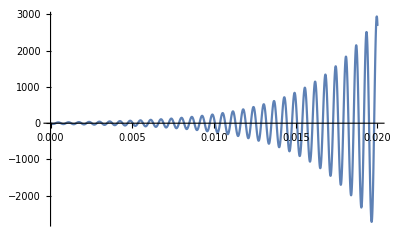

```mathematica
Rb=1005;
gr2=Show[Plot[respuesta,{t,0,0.02},PlotRange-> All]]
```

```mathematica
0.5*10^-3
```

0.0005